```mathematica
ClearAll["Global`*"]
ClearSystemCache[]
$PrePrint=MatrixForm;
```

```mathematica
SetDirectory[ToString[NotebookDirectory[]]<>"/BasisData"];
```

```mathematica
nA=1;
nB=1;
g=1.0;
emax=50;
stride=nA+nB;
eGS=Sum[0.5+i,{i,0,nA-1}]+Sum[0.5+i,{i,0,nB-1}];
(*diagonalize matrix build with states with energy ≤ eset*)
eset=35;
lastRangeIndex=eset-eGS+1;
```

```mathematica
name="H_nA="<>ToString[nA]<>"_nB="<>ToString[nB]<>"_Emax="<>ToString[emax];
ranges=Import[name<>".basisrange","Table"];
ranges=Table[ranges[[i,1]],{i,Length[ranges]}];

basis=Import[name<>".basis","Table"];
data=Import[name<>".integrals","Table"];
dataRanges=Import[name<>".integralsrange","Table"];
```

```mathematica
matrix=Table[0,{i,ranges[[lastRangeIndex]]},{j,ranges[[lastRangeIndex]]}];
```

```mathematica
For[i=1,i<=dataRanges[[lastRangeIndex]][[1]],i++,
matrix[[ data[[i]][[1]],data[[i]][[2]] ]]=g*data[[i]][[3]];
matrix[[ data[[i]][[2]],data[[i]][[1]] ]]=g*data[[i]][[3]];
If[data[[i]][[1]]==data[[i]][[2]],
matrix[[data[[i]][[1]],data[[i]][[2]]]]+=Sum[0.5+basis[[data[[i]][[1]]]][[j]], {j,nA}]+Sum[0.5+basis[[data[[i]][[1]]]][[j]], {j,nA+1,stride}];]
];
```

```mathematica
Eigenvalues[matrix,-1]
```

(1.31969)

```mathematica
vecGS=Eigenvectors[matrix][[-1]];
Osc[k_,x_]:=HermiteH[k,x]Exp[-x^2/2]/Pi^(1/4)/Sqrt[2^k*Factorial[k]]
gs[x_,y_]:=Sum[vecGS[[i]]*Osc[basis[[i]][[1]],x]*Osc[basis[[i]][[2]],y],{i,ranges[[lastRangeIndex]]}]
```

```mathematica
exactsol=FindRoot[2*Sqrt[2]*Gamma[-x/2+3/4]+g*Gamma[-x/2+1/4]==0, {x,1.2}];
exactene=x /.exactsol;
coeffs=Table[Osc[i,0]/((0.5+i)-exactene), {i,0,70}];
exactene+=0.5
relgs[x_]:=Sum[coeffs[[i]]*Osc[i-1,x],{i,1,71}];
norm=Sum[coeffs[[i]]^2,{i,1,71}];
exactgs[x_,y_]:=relgs[(x-y)/Sqrt[2]]*Osc[0,(x+y)/Sqrt[2]]/Sqrt[norm];
```

1.30675

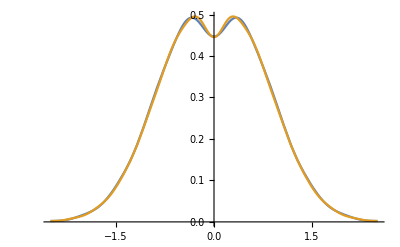

```mathematica
Plot[{-gs[x,-x],-exactgs[x,-x]}, {x,-2.5,2.5}]
```